Autor: Antoni Perużyński

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 1

Metody Rungego-Kutty

Napisać procedury realizujące algorytmy metod Rungego-Kutty rzędu trzeciego i rzędu czwartego (argumenty:  f, x_0, y_0, h, n).

Korzystając z napisanych procedur wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=(x y(x) - y^2(x))/x^2,
y(1)=2.

Obliczenia wykonać dla 20 kroków o długości 0.1.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.

## Rozwiązanie

### Tworzenie procedur

```mathematica
RungeKuttyThree[function_,X0_,Y0_,H_,number_]:=Module[{f=function,x0=X0, y0=Y0,h=H, n=number },
xList ={x0};
yList = {y0};

For[i=1, i≤n, i++,
AppendTo[xList,xList[[i] ]+h];
k1=f[xList[[i]],yList[[i]]];
k2=f[xList[[i]]+0.5*h,yList[[i]]+0.5*h*k1];
k3 = f[xList[[i+1]], yList[[i]]-h*k1+2*h*k2];
AppendTo[yList,yList[[i] ]+1/6*h*(k1+4*k2+k3)];
];
Return[Transpose[{xList,yList}]]
]

f[x_,y_] := (x*y-y^2)/x^2;
rK3Points = RungeKuttyThree[f,1,2,0.1,20];
```

```mathematica
RungeKuttyFour[function_,X0_,Y0_,H_,number_]:=Module[{f=function,x0=X0, y0=Y0,h=H, n=number },
xList ={x0};
yList = {y0};

For[i=1, i≤n, i++,
AppendTo[xList,xList[[i] ]+h];
k1=f[xList[[i]],yList[[i]]];
k2=f[xList[[i]]+0.5*h,yList[[i]]+0.5*h*k1];
k3=f[xList[[i]]+0.5*h,yList[[i]]+0.5*h*k2];
k4= f[xList[[i+1]], yList[[i]]+h*k3];
AppendTo[yList,yList[[i] ]+1/6*h*(k1+2*k2+2*k3+k4)];
];
Return[Transpose[{xList,yList}]]
]

f[x_,y_] :=  (x*y-y^2)/x^2;
rK4Points =RungeKuttyFour[f,1,2,0.1,20];
```

### Wykresy przedstawiające wyniki działania procedur

```mathematica
p1=ListPlot[rK3Points,PlotStyle->Red ];
p2 =ListPlot[rK4Points, PlotStyle->Green];
Show[p2,p1]
```

-Graphics-

### Obliczenie rozwiązania dokładnego oraz narysowanie wykresu z wynikiem dokładnym oraz przybliżonymi

```mathematica
accResult=DSolve[{y'[x] == (x*y[x] -y[x]^2)/x^2, y[1]==2} , y[x], x];
p3=Plot[accResult[[1,1,2]],{x,1,3}];
Show[p1,p2,p3]
```

-Graphics-

### Obliczanie błędów względnych oraz wykreślenie ich na wykresie

```mathematica
xw=Transpose[rK4Points][[1]] ;
yw3=Transpose[rK3Points][[2]];
yw4=Transpose[rK4Points][[2]];
```

```mathematica
accResultPoints = Table[accResult[[1, 1, 2]] /. {x -> xw[[i]]}, {i, 1,  Length[xw]}];
bladbezwzgledny3 = Abs[yw3 - accResultPoints] ;
bladwzgledny3 = 100 * bladbezwzgledny3 /Abs[accResultPoints] ;
b1=BarChart[bladwzgledny3, ChartStyle->Black];
```

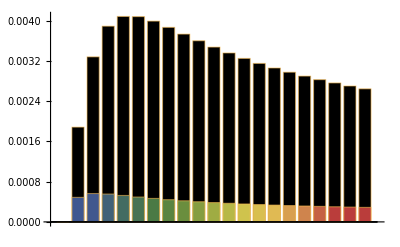

```mathematica
bladbezwzgledny4 = Abs[yw4 - accResultPoints] ;
bladwzgledny4 = 100 * bladbezwzgledny4 /Abs[accResultPoints] ;
b2=BarChart[bladwzgledny4,ChartStyle->"DarkRainbow"];
Show[b1,b2, PlotLegends->Automatic]
```